```mathematica
randomDirection:=Module[{cosTheta,sinTheta,phi},
cosTheta=RandomReal[{-1,1}];
phi=RandomReal[2π];
sinTheta=√(1-cosTheta^2);
{cosTheta,sinTheta Sin[phi],sinTheta Cos[phi]}];
scatterE[erg0_]:=Module[{vecVn,vecVp,vecVcm,vecVnout,mn=939.565,mp=938.272,kT=2.53*^-8},
vecVn={√(2 erg0/mn),0,0};
vecVp=RandomVariate[NormalDistribution[0,√(kT/mp)],3];
vecVcm=-(mn vecVn+mp vecVp)/(mn+mp);
vecVnout=Norm[vecVn+vecVcm]randomDirection-vecVcm;
1/2 mn vecVnout.vecVnout];
```

```mathematica
Table[scatterE[2.53*^-8],10]
```

{8.06772×10^-9,3.38112×10^-8,7.55591×10^-9,2.18354×10^-8,1.82788×10^-8,3.42735×10^-8,5.13065×10^-8,4.039×10^-8,7.06348×10^-8,1.21449×10^-8}

```mathematica
Table[randomDirection,10]
```

{{0.062651,-0.745959,0.663038},{-0.0053444,-0.361151,0.932492},{0.66368,-0.142942,-0.734232},{-0.75214,0.658861,0.0136935},{-0.509039,0.640629,-0.574869},{-0.464078,0.63415,-0.618454},{-0.555852,0.648375,0.520229},{-0.962703,-0.160452,-0.21785},{-0.413439,-0.670265,-0.61629},{0.587195,0.609733,-0.532379}}

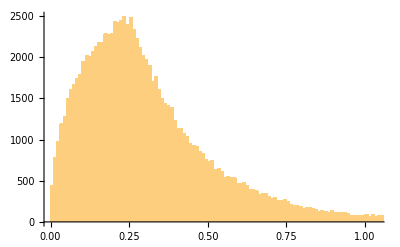

```mathematica
Histogram[Table[scatterE[2.53*^-8],100000],{1*^-9}]
```

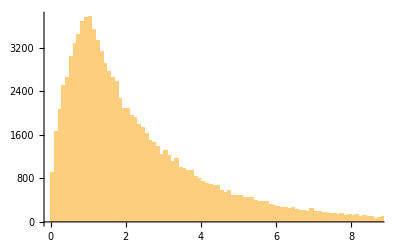

```mathematica
Histogram[Table[scatterE[1.0*^-8],100000],{1*^-9}]
```

```mathematica
hlist1=HistogramList[Table[scatterE[2.53*^-8],1000000],{1.0*^-9}];
```

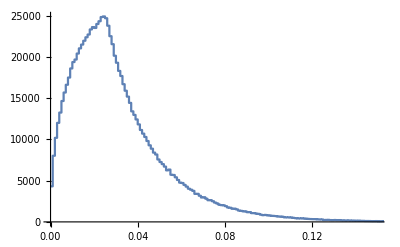

```mathematica
ListStepPlot[Transpose[{10^6 Drop[hlist1[[1]],-1],hlist1[[2]]}],PlotRange->{{0,0.15},All}]
```

```mathematica
plotData[hlist_,f_]:=Transpose[{10^6 Drop[hlist[[1]],-1],f hlist[[2]]/Total[hlist[[2]]]}];
```

```mathematica
factor = 0.082572 0.025 csElasticH[2.53*^-8]/(4π 20.5^2)
```

0.0000117585

```mathematica
data1=plotData[hlist1,factor];
```

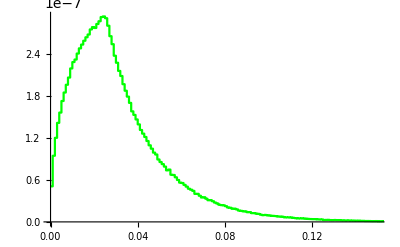

```mathematica
plot1=ListStepPlot[data1,PlotRange->{{0,0.15},All},PlotStyle->Green]
```

```mathematica
csElasticH=Interpolation[ImportString["1.00000000e-10      3.67426e+02
1.03125000e-10      3.61831e+02
1.06250000e-10      3.56485e+02
1.09375000e-10      3.51370e+02
1.12500000e-10      3.46470e+02
1.15625000e-10      3.41770e+02
1.18750000e-10      3.37257e+02
1.21875000e-10      3.32918e+02
1.25000000e-10      3.28744e+02
1.28125000e-10      3.24724e+02
1.31250000e-10      3.20848e+02
1.34375000e-10      3.17108e+02
1.37500000e-10      3.13497e+02
1.43750000e-10      3.06631e+02
1.50000000e-10      3.00199e+02
1.56250000e-10      2.94158e+02
1.62500000e-10      2.88470e+02
1.68750000e-10      2.83100e+02
1.75000000e-10      2.78022e+02
1.81250000e-10      2.73209e+02
1.87500000e-10      2.68639e+02
1.93750000e-10      2.64292e+02
2.00000000e-10      2.60151e+02
2.09375000e-10      2.54291e+02
2.18750000e-10      2.48813e+02
2.28125000e-10      2.43677e+02
2.37500000e-10      2.38848e+02
2.46875000e-10      2.34298e+02
2.56250000e-10      2.30000e+02
2.65625000e-10      2.25933e+02
2.75000000e-10      2.22076e+02
2.84375000e-10      2.18411e+02
2.93750000e-10      2.14924e+02
3.03125000e-10      2.11600e+02
3.12500000e-10      2.08428e+02
3.21875000e-10      2.05395e+02
3.31250000e-10      2.02492e+02
3.40625000e-10      1.99711e+02
3.50000000e-10      1.97042e+02
3.59375000e-10      1.94479e+02
3.68750000e-10      1.92014e+02
3.78125000e-10      1.89642e+02
3.87500000e-10      1.87357e+02
3.96875000e-10      1.85154e+02
4.06250000e-10      1.83027e+02
4.25000000e-10      1.78988e+02
4.43750000e-10      1.75209e+02
4.62500000e-10      1.71662e+02
4.81250000e-10      1.68326e+02
5.00000000e-10      1.65180e+02
5.15625000e-10      1.62691e+02
5.31250000e-10      1.60314e+02
5.46875000e-10      1.58039e+02
5.62500000e-10      1.55860e+02
5.78125000e-10      1.53771e+02
5.93750000e-10      1.51765e+02
6.09375000e-10      1.49837e+02
6.25000000e-10      1.47982e+02
6.40625000e-10      1.46196e+02
6.56250000e-10      1.44474e+02
6.71875000e-10      1.42814e+02
6.87500000e-10      1.41210e+02
7.18750000e-10      1.38162e+02
7.50000000e-10      1.35308e+02
7.81250000e-10      1.32628e+02
8.12500000e-10      1.30105e+02
8.43750000e-10      1.27724e+02
8.75000000e-10      1.25474e+02
9.06250000e-10      1.23341e+02
9.37500000e-10      1.21317e+02
9.68750000e-10      1.19392e+02
1.00000000e-09      1.17559e+02
1.03125000e-09      1.15811e+02
1.06250000e-09      1.14141e+02
1.09375000e-09      1.12544e+02
1.12500000e-09      1.11015e+02
1.15625000e-09      1.09548e+02
1.18750000e-09      1.08140e+02
1.21875000e-09      1.06788e+02
1.25000000e-09      1.05487e+02
1.28125000e-09      1.04234e+02
1.31250000e-09      1.03027e+02
1.34375000e-09      1.01863e+02
1.37500000e-09      1.00739e+02
1.43750000e-09      9.86033e+01
1.50000000e-09      9.66042e+01
1.56250000e-09      9.47279e+01
1.62500000e-09      9.29623e+01
1.68750000e-09      9.12971e+01
1.75000000e-09      8.97232e+01
1.81250000e-09      8.82326e+01
1.87500000e-09      8.68183e+01
1.93750000e-09      8.54741e+01
2.00000000e-09      8.41944e+01
2.09375000e-09      8.23853e+01
2.18750000e-09      8.06958e+01
2.28125000e-09      7.91134e+01
2.37500000e-09      7.76275e+01
2.46875000e-09      7.62287e+01
2.56250000e-09      7.49090e+01
2.65625000e-09      7.36613e+01
2.75000000e-09      7.24794e+01
2.84375000e-09      7.13578e+01
2.93750000e-09      7.02915e+01
3.03125000e-09      6.92764e+01
3.12500000e-09      6.83084e+01
3.21875000e-09      6.73841e+01
3.31250000e-09      6.65005e+01
3.40625000e-09      6.56545e+01
3.50000000e-09      6.48438e+01
3.59375000e-09      6.40659e+01
3.68750000e-09      6.33187e+01
3.78125000e-09      6.26004e+01
3.87500000e-09      6.19091e+01
3.96875000e-09      6.12433e+01
4.06250000e-09      6.06014e+01
4.25000000e-09      5.93840e+01
4.43750000e-09      5.82473e+01
4.62500000e-09      5.71830e+01
4.81250000e-09      5.61839e+01
5.00000000e-09      5.52437e+01
5.15625000e-09      5.45013e+01
5.31250000e-09      5.37933e+01
5.46875000e-09      5.31171e+01
5.62500000e-09      5.24706e+01
5.78125000e-09      5.18517e+01
5.93750000e-09      5.12585e+01
6.09375000e-09      5.06894e+01
6.25000000e-09      5.01428e+01
6.40625000e-09      4.96174e+01
6.56250000e-09      4.91118e+01
6.71875000e-09      4.86249e+01
6.87500000e-09      4.81555e+01
7.18750000e-09      4.72658e+01
7.50000000e-09      4.64354e+01
7.81250000e-09      4.56583e+01
8.12500000e-09      4.49292e+01
8.43750000e-09      4.42436e+01
8.75000000e-09      4.35976e+01
9.06250000e-09      4.29875e+01
9.37500000e-09      4.24103e+01
9.68750000e-09      4.18634e+01
1.00000000e-08      4.13442e+01
1.03125000e-08      4.08506e+01
1.06250000e-08      4.03807e+01
1.09375000e-08      3.99328e+01
1.12500000e-08      3.95052e+01
1.15625000e-08      3.90965e+01
1.18750000e-08      3.87055e+01
1.21875000e-08      3.83310e+01
1.25000000e-08      3.79720e+01
1.28125000e-08      3.76274e+01
1.31250000e-08      3.72964e+01
1.34375000e-08      3.69781e+01
1.37500000e-08      3.66718e+01
1.43750000e-08      3.60926e+01
1.50000000e-08      3.55538e+01
1.56250000e-08      3.50512e+01
1.62500000e-08      3.45811e+01
1.68750000e-08      3.41405e+01
1.75000000e-08      3.37265e+01
1.81250000e-08      3.33368e+01
1.87500000e-08      3.29693e+01
1.93750000e-08      3.26220e+01
2.00000000e-08      3.22933e+01
2.06625000e-08      3.19636e+01
2.13250000e-08      3.16516e+01
2.19875000e-08      3.13558e+01
2.26500000e-08      3.10751e+01
2.33125000e-08      3.08082e+01
2.39750000e-08      3.05542e+01
2.46375000e-08      3.03122e+01
2.53000000e-08      3.00812e+01
2.64578200e-08      2.97021e+01
2.76156300e-08      2.93512e+01
2.87734400e-08      2.90253e+01
2.99312500e-08      2.87220e+01
3.10890700e-08      2.84389e+01
3.22468800e-08      2.81741e+01
3.34046900e-08      2.79258e+01
3.45625000e-08      2.76927e+01
3.55273500e-08      2.75089e+01
3.64921900e-08      2.73340e+01
3.74570400e-08      2.71674e+01
3.84218800e-08      2.70084e+01
3.93867300e-08      2.68566e+01
4.03515700e-08      2.67114e+01
4.13164100e-08      2.65725e+01
4.22812500e-08      2.64395e+01
4.42109400e-08      2.61897e+01
4.61406300e-08      2.59594e+01
4.80703200e-08      2.57464e+01
5.00000000e-08      2.55489e+01
5.15625000e-08      2.53991e+01
5.31250000e-08      2.52578e+01
5.46875000e-08      2.51240e+01
5.62500000e-08      2.49974e+01
5.78125000e-08      2.48773e+01
5.93750000e-08      2.47632e+01
6.09375000e-08      2.46547e+01
6.25000000e-08      2.45515e+01
6.40625000e-08      2.44531e+01
6.56250000e-08      2.43592e+01
6.71875000e-08      2.42695e+01
6.87500000e-08      2.41838e+01
7.18750000e-08      2.40232e+01
7.50000000e-08      2.38756e+01
7.81250000e-08      2.37395e+01
8.12500000e-08      2.36137e+01
8.43750000e-08      2.34970e+01
8.75000000e-08      2.33885e+01
9.06250000e-08      2.32873e+01
9.37500000e-08      2.31928e+01
9.68750000e-08      2.31044e+01
1.00000000e-07      2.30213e+01
1.03125000e-07      2.29433e+01
1.06250000e-07      2.28698e+01
1.09375000e-07      2.28005e+01
1.12500000e-07      2.27350e+01
1.15625000e-07      2.26730e+01
1.18750000e-07      2.26142e+01
1.21875000e-07      2.25585e+01
1.25000000e-07      2.25055e+01
1.28125000e-07      2.24551e+01
1.31250000e-07      2.24071e+01
1.34375000e-07      2.23613e+01
1.37500000e-07      2.23175e+01
1.43750000e-07      2.22358e+01
1.50000000e-07      2.21609e+01
1.56250000e-07      2.20919e+01
1.62500000e-07      2.20282e+01
1.68750000e-07      2.19693e+01
1.75000000e-07      2.19145e+01
1.81250000e-07      2.18635e+01
1.87500000e-07      2.18160e+01
1.93750000e-07      2.17715e+01
2.00000000e-07      2.17297e+01
2.09375000e-07      2.16718e+01
2.18750000e-07      2.16188e+01
2.28125000e-07      2.15702e+01
2.37500000e-07      2.15255e+01
2.46875000e-07      2.14841e+01
2.56250000e-07      2.14457e+01
2.65625000e-07      2.14101e+01
2.75000000e-07      2.13769e+01
2.84375000e-07      2.13459e+01
2.93750000e-07      2.13168e+01
3.03125000e-07      2.12896e+01
3.12500000e-07      2.12640e+01
3.21875000e-07      2.12399e+01
3.31250000e-07      2.12171e+01
3.40625000e-07      2.11956e+01
3.50000000e-07      2.11753e+01
3.59375000e-07      2.11560e+01
3.68750000e-07      2.11377e+01
3.78125000e-07      2.11203e+01
3.87500000e-07      2.11037e+01
3.96875000e-07      2.10880e+01
4.06250000e-07      2.10729e+01
4.25000000e-07      2.10448e+01
4.43750000e-07      2.10191e+01
4.62500000e-07      2.09954e+01
5.00000000e-07      2.09535e+01
5.31250000e-07      2.09230e+01
5.62500000e-07      2.08960e+01
5.93750000e-07      2.08718e+01
6.25000000e-07      2.08500e+01
6.87500000e-07      2.08123e+01
7.50000000e-07      2.07810e+01
8.12500000e-07      2.07544e+01
8.75000000e-07      2.07317e+01
9.37500000e-07      2.07119e+01
1.00000000e-06      2.06947e+01
1.06250000e-06      2.06795e+01","Table"]];
```

```mathematica
csElasticH[2.53*^-8]
```

30.0812

```mathematica
hlist1
```

{{0.,1.×10^-9,2.×10^-9,3.×10^-9,4.×10^-9,5.×10^-9,6.×10^-9,7.×10^-9,8.×10^-9,9.×10^-9,1.×10^-8,1.1×10^-8,1.2×10^-8,1.3×10^-8,1.4×10^-8,1.5×10^-8,1.6×10^-8,1.7×10^-8,1.8×10^-8,1.9×10^-8,2.×10^-8,2.1×10^-8,2.2×10^-8,2.3×10^-8,2.4×10^-8,2.5×10^-8,2.6×10^-8,2.7×10^-8,2.8×10^-8,2.9×10^-8,3.×10^-8,3.1×10^-8,3.2×10^-8,3.3×10^-8,3.4×10^-8,3.5×10^-8,3.6×10^-8,3.7×10^-8,3.8×10^-8,3.9×10^-8,4.×10^-8,4.1×10^-8,4.2×10^-8,4.3×10^-8,4.4×10^-8,4.5×10^-8,4.6×10^-8,4.7×10^-8,4.8×10^-8,4.9×10^-8,5.×10^-8,5.1×10^-8,5.2×10^-8,5.3×10^-8,5.4×10^-8,5.5×10^-8,5.6×10^-8,5.7×10^-8,5.8×10^-8,5.9×10^-8,6.×10^-8,6.1×10^-8,6.2×10^-8,6.3×10^-8,6.4×10^-8,6.5×10^-8,6.6×10^-8,6.7×10^-8,6.8×10^-8,6.9×10^-8,7.×10^-8,7.1×10^-8,7.2×10^-8,7.3×10^-8,7.4×10^-8,7.5×10^-8,7.6×10^-8,7.7×10^-8,7.8×10^-8,7.9×10^-8,8.×10^-8,8.1×10^-8,8.2×10^-8,8.3×10^-8,8.4×10^-8,8.5×10^-8,8.6×10^-8,8.7×10^-8,8.8×10^-8,8.9×10^-8,9.×10^-8,9.1×10^-8,9.2×10^-8,9.3×10^-8,9.4×10^-8,9.5×10^-8,9.6×10^-8,9.7×10^-8,9.8×10^-8,9.9×10^-8,1.×10^-7,1.01×10^-7,1.02×10^-7,1.03×10^-7,1.04×10^-7,1.05×10^-7,1.06×10^-7,1.07×10^-7,1.08×10^-7,1.09×10^-7,1.1×10^-7,1.11×10^-7,1.12×10^-7,1.13×10^-7,1.14×10^-7,1.15×10^-7,1.16×10^-7,1.17×10^-7,1.18×10^-7,1.19×10^-7,1.2×10^-7,1.21×10^-7,1.22×10^-7,1.23×10^-7,1.24×10^-7,1.25×10^-7,1.26×10^-7,1.27×10^-7,1.28×10^-7,1.29×10^-7,1.3×10^-7,1.31×10^-7,1.32×10^-7,1.33×10^-7,1.34×10^-7,1.35×10^-7,1.36×10^-7,1.37×10^-7,1.38×10^-7,1.39×10^-7,1.4×10^-7,1.41×10^-7,1.42×10^-7,1.43×10^-7,1.44×10^-7,1.45×10^-7,1.46×10^-7,1.47×10^-7,1.48×10^-7,1.49×10^-7,1.5×10^-7,1.51×10^-7,1.52×10^-7,1.53×10^-7,1.54×10^-7,1.55×10^-7,1.56×10^-7,1.57×10^-7,1.58×10^-7,1.59×10^-7,1.6×10^-7,1.61×10^-7,1.62×10^-7,1.63×10^-7,1.64×10^-7,1.65×10^-7,1.66×10^-7,1.67×10^-7,1.68×10^-7,1.69×10^-7,1.7×10^-7,1.71×10^-7,1.72×10^-7,1.73×10^-7,1.74×10^-7,1.75×10^-7,1.76×10^-7,1.77×10^-7,1.78×10^-7,1.79×10^-7,1.8×10^-7,1.81×10^-7,1.82×10^-7,1.83×10^-7,1.84×10^-7,1.85×10^-7,1.86×10^-7,1.87×10^-7,1.88×10^-7,1.89×10^-7,1.9×10^-7,1.91×10^-7,1.92×10^-7,1.93×10^-7,1.94×10^-7,1.95×10^-7,1.96×10^-7,1.97×10^-7,1.98×10^-7,1.99×10^-7,2.×10^-7,2.01×10^-7,2.02×10^-7,2.03×10^-7,2.04×10^-7,2.05×10^-7,2.06×10^-7,2.07×10^-7,2.08×10^-7,2.09×10^-7,2.1×10^-7,2.11×10^-7,2.12×10^-7,2.13×10^-7,2.14×10^-7,2.15×10^-7,2.16×10^-7,2.17×10^-7,2.18×10^-7,2.19×10^-7,2.2×10^-7,2.21×10^-7,2.22×10^-7,2.23×10^-7,2.24×10^-7,2.25×10^-7,2.26×10^-7,2.27×10^-7,2.28×10^-7,2.29×10^-7,2.3×10^-7,2.31×10^-7,2.32×10^-7,2.33×10^-7,2.34×10^-7,2.35×10^-7,2.36×10^-7,2.37×10^-7,2.38×10^-7,2.39×10^-7,2.4×10^-7,2.41×10^-7,2.42×10^-7,2.43×10^-7,2.44×10^-7,2.45×10^-7,2.46×10^-7,2.47×10^-7,2.48×10^-7,2.49×10^-7,2.5×10^-7,2.51×10^-7,2.52×10^-7,2.53×10^-7,2.54×10^-7,2.55×10^-7,2.56×10^-7,2.57×10^-7,2.58×10^-7,2.59×10^-7,2.6×10^-7,2.61×10^-7,2.62×10^-7,2.63×10^-7,2.64×10^-7,2.65×10^-7,2.66×10^-7,2.67×10^-7,2.68×10^-7,2.69×10^-7,2.7×10^-7,2.71×10^-7,2.72×10^-7,2.73×10^-7,2.74×10^-7,2.75×10^-7,2.76×10^-7,2.77×10^-7,2.78×10^-7,2.79×10^-7,2.8×10^-7,2.81×10^-7,2.82×10^-7,2.83×10^-7,2.84×10^-7,2.85×10^-7,2.86×10^-7,2.87×10^-7,2.88×10^-7,2.89×10^-7,2.9×10^-7,2.91×10^-7,2.92×10^-7,2.93×10^-7,2.94×10^-7,2.95×10^-7,2.96×10^-7,2.97×10^-7,2.98×10^-7,2.99×10^-7,3.×10^-7,3.01×10^-7,3.02×10^-7,3.03×10^-7,3.04×10^-7,3.05×10^-7,3.06×10^-7,3.07×10^-7,3.08×10^-7,3.09×10^-7,3.1×10^-7,3.11×10^-7,3.12×10^-7,3.13×10^-7,3.14×10^-7,3.15×10^-7,3.16×10^-7,3.17×10^-7,3.18×10^-7,3.19×10^-7,3.2×10^-7,3.21×10^-7,3.22×10^-7,3.23×10^-7,3.24×10^-7,3.25×10^-7,3.26×10^-7,3.27×10^-7,3.28×10^-7,3.29×10^-7,3.3×10^-7,3.31×10^-7,3.32×10^-7,3.33×10^-7,3.34×10^-7,3.35×10^-7,3.36×10^-7,3.37×10^-7,3.38×10^-7,3.39×10^-7,3.4×10^-7,3.41×10^-7,3.42×10^-7,3.43×10^-7,3.44×10^-7,3.45×10^-7,3.46×10^-7,3.47×10^-7,3.48×10^-7,3.49×10^-7,3.5×10^-7,3.51×10^-7,3.52×10^-7,3.53×10^-7,3.54×10^-7,3.55×10^-7,3.56×10^-7,3.57×10^-7},{4312,8020,10194,12009,13257,14659,15689,16629,17505,18608,19381,19688,20415,21043,21502,21965,22387,22723,23339,23621,23518,23999,24333,24843,24912,24698,23789,22520,21551,20150,19299,18311,17692,16699,15906,15191,14433,13406,12975,12425,11824,11146,10702,10298,9809,9288,8877,8400,8172,7571,7261,7006,6705,6249,6345,5717,5687,5408,5083,4761,4718,4487,4277,4025,3901,3762,3399,3403,3171,2958,2992,2811,2628,2640,2507,2340,2231,2079,2030,2011,1904,1745,1714,1588,1607,1519,1373,1339,1279,1272,1175,1185,1063,1066,999,969,879,816,846,797,779,738,723,700,646,652,624,550,552,554,532,489,450,420,424,439,403,385,358,345,334,333,302,303,294,232,238,248,220,209,229,209,217,184,171,176,171,172,156,151,135,151,123,126,108,108,104,93,90,98,72,83,81,86,77,73,75,60,71,55,56,52,45,46,45,50,42,50,51,39,43,38,32,25,39,37,17,22,23,30,34,36,23,19,19,15,20,23,21,11,11,16,13,9,18,4,11,17,9,14,14,10,14,13,12,9,10,9,6,9,3,5,8,9,7,5,4,12,2,5,9,5,2,2,5,2,6,5,7,2,4,2,3,3,3,1,2,2,2,3,2,3,0,2,3,1,4,2,0,2,1,1,0,1,0,1,2,1,1,3,1,1,0,1,2,0,1,0,0,0,0,0,0,2,1,0,0,0,0,0,1,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}}